```mathematica
Exit
```

```mathematica
Get[
FileNameJoin[{ParentDirectory[NotebookDirectory[]],"CycleSamplerLink.m"}]
]
```

/Users/Henrik/github/CycleSamplerLink/LibraryResources/MacOSX-ARM64/SampleRandomVariable_3D.dylib

Compiling cSampleRandomVariable[3]...

/Users/Henrik/github/CycleSamplerLink/LibraryResources/Source/SampleRandomVariable_3D.cpp

Compilation done. Time elapsed = 1.12321 s.

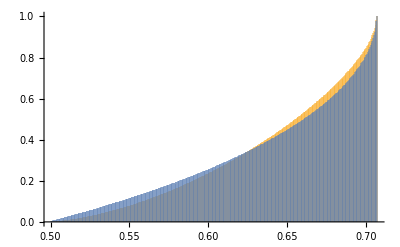

```mathematica
data1=CycleSample["Gyradius",3,{1,1,1,1},1000000,"QuotientSpace"->False];
data2=CycleSample["Gyradius",3,{1,1,1,1},1000000,"QuotientSpace"->True];
Histogram[{data1,data2},"Wand","CDF",PlotRange->All]
```

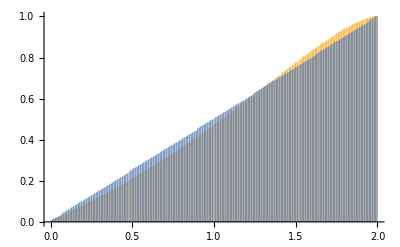

```mathematica
data1=CycleSampleChordLength[3,{1,1,1,1},{1,3},1000000,"QuotientSpace"->False];
data2=CycleSampleChordLength[3,{1,1,1,1},{1,3},1000000,"QuotientSpace"->True];
Histogram[{data1,data2},"Wand","CDF",PlotRange->All]
```